# Analysing results from backward evolution (RiverSim)

## JSON functions

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
ImportJSONData[files_]:=Module[{},
Switch[Head[files],
String,
Import[files,"RawJSON"],
List,
Import[#,"RawJSON"]&/@files
]
];
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

## Defining functions

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
angDevColumn=1;
geoDevColumn=2;
a1Column=3;
a2Column=4;
```

```mathematica
initialization[etaOrigin_, etaMin_, etaMax_,experimentName_,fileName_:"/back_lap"]:=Module[{},
etaOriginal = etaOrigin;
folder=experimentName<>"/original_eta" <> ToString@etaOriginal;

(*etaRange={0.4,0.6,0.7,0.8,0.9,1,1.2,1.3,1.4,1.5,1.6,1.7,2.3(*,2.7,2.8,2.9,3,3.1,3.3,3.4,3.6,3.7,3.9*)};
etaMin=0;
etaMax=Length@etaRange-1;*)

etaRange=Range[etaMin,etaMax];
(*If[etaOriginal<=7,
etaRange=Range[etaMin,etaMax],
etaRange=Join[Range[etaMin,etaOrigin-0.5],Table[etaOrigin+i,{i,{-0.5,-0.25,0,0.25,0.5}}],Range[etaOrigin+1,etaMax]]];*)


backwardSimFilePaths = Table[folder<>fileName<>ToString[eta]<>".json",{eta, etaRange}];
backwardSimDataArray=ImportJSONData[backwardSimFilePaths];
etaOriginal = etaOriginal/10.;
etaRange =etaRange/10.;
]
```

### Geometric deviation

#### Importing data, some statistics and log scale

```mathematica
plotGeoDev[streamMin_,streamMax_, stepMin_, stepMax_]:=Module[{},
Print[Reap[Do[If[stepMax>Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]],Sow[i/10.]],{i,1, etaRange//Length}];"Number of steps exceeded in eta = " ]];

geoDev = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];

(*LOG SCALE*)
geoDevLog = Table[{etaRange[[i]], Log@Quantile[Abs@Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}]/.{Indeterminate->-25};

(*PLOTS*)
geoDevPlot=ListLinePlot[geoDev,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Odchylenie geometryczne",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
geoDevLogPLot=ListLinePlot[geoDevLog,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotRange->All,PlotLabel->"|Odchylenie geometryczne| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Width of geometric deviation

```mathematica
plotGeoDevWidth:=Module[{},
geoDevWidth=geoDev[[2]];
geoDevWidth[[All,2]]=geoDev[[3,All,2]]-geoDev[[1,All,2]];geoDevWidthPlot=ListLinePlot[{geoDevWidth},(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*)(*PlotRange->All,*)PlotLabel->"Szerokość odchylenia geometrycznego",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];

(* Width of geometric deviation in logarithmic scale *)
geoDevWidthLog=geoDevWidth;
geoDevWidthLog[[All,2]]=Log@Abs@geoDevWidth[[All,2]]/.{Indeterminate->-25};
geoDevWidthLogPlot=ListLinePlot[{geoDevWidthLog},(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*)PlotRange->All,PlotLabel->"|Szerokość odchylenia geometrycznego| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Metrics: sum of squares

```mathematica
plotGeoDev[streamMin_,streamMax_, stepMin_, stepMax_]:=Module[{},
Print[Reap[Do[If[stepMax>Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]],Sow[i/10.]],{i,1, etaRange//Length}];"Number of steps exceeded in eta = " ]];

geoDev = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];

(*LOG SCALE*)
geoDevLog = Table[{etaRange[[i]], Log@Quantile[Abs@Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, geoDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,geoDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}]/.{Indeterminate->-25};

(*PLOTS*)
geoDevPlot=ListLinePlot[geoDev,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Odchylenie geometryczne",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
geoDevLogPLot=ListLinePlot[geoDevLog,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotRange->All,PlotLabel->"|Odchylenie geometryczne| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Geometric deviation: final results

{Number of steps exceeded in eta = ,{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}}}

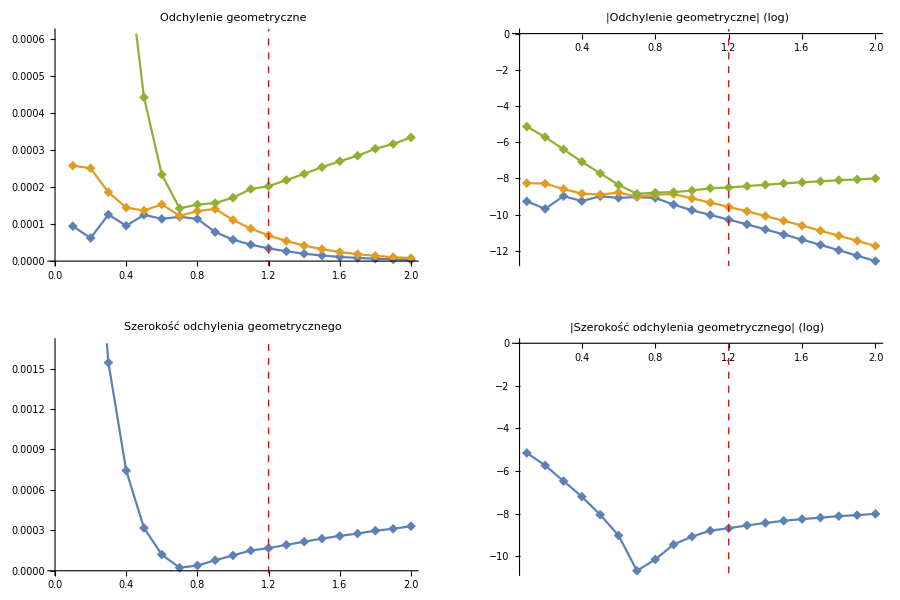

```mathematica
plotGeoDev[1,2,1,25]
plotGeoDevWidth
GraphicsGrid[{{geoDevPlot,geoDevLogPLot},{geoDevWidthPlot,geoDevWidthLogPlot}},Frame->All,ImageSize->900,AspectRatio->1/1.5]
```

### Angular deviation

#### Importing data, some statistics and log scale

```mathematica
plotAngDev[streamMin_,streamMax_, stepMin_, stepMax_]:=Module[{},
(*Print[Reap[Do[If[stepMax>Length@backwardSimDataArray[[i,3,1,1,2,angDevColumn]],Sow[i/10.]],{i,1, etaRange//Length}];"Number of steps exceeded in eta = " ]];*)

angDev = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, angDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,angDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];

(*LOG SCALE*)
angDevLog = Table[{etaRange[[i]], Log@Quantile[Abs@Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, angDevColumn]][[All,stepMin;;If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,angDevColumn]], stepMax,-1]]]/.{Null->0.}],q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}]/.{Indeterminate->-25};

(*PLOTS*)
angDevPlot=ListLinePlot[angDev,(*PlotRange->All,*)(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Odchylenie kątowe",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
angDevLogPLot=ListLinePlot[angDevLog, (*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotRange->All,PlotLabel->"|Odchylenie kątowe| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Width of angular deviation

```mathematica
plotAngDevWidth:=Module[{},
angDevWidth=angDev[[2]];
angDevWidth[[All,2]]=angDev[[3,All,2]]-angDev[[2,All,2]];angDevWidthPlot=ListLinePlot[{angDevWidth},(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*)(*PlotRange->All,*)PlotLabel->"Szerokość odchylenia kątowego",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];

(* Width of geometric deviation in logarithmic scale *)
angDevWidthLog=angDevWidth;
angDevWidthLog[[All,2]]=Log@Abs@angDevWidth[[All,2]]/.{Indeterminate->-25};angDevWidthLogPlot=ListLinePlot[{angDevWidthLog},(*PlotLegends->Placed[{"Width of geometric deviation"},{0.35,0.75}],*)PlotRange->All,PlotLabel->"|Szerokość odchylenia kątowego| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### Geometric deviation: final results

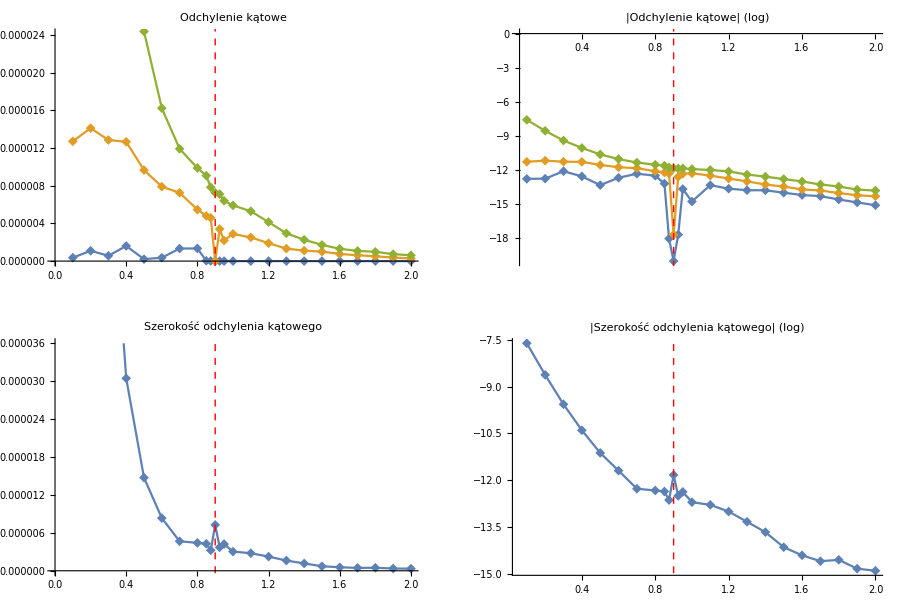

```mathematica
plotAngDev[1,2,1,25]
plotAngDevWidth
GraphicsGrid[{{angDevPlot,angDevLogPLot},{angDevWidthPlot,angDevWidthLogPlot}},Frame->All,ImageSize->900,AspectRatio->1/1.5]
```

### Coefficients a1, a2, a3

#### Normalised a2 (a2/a1^2) and log scale

```mathematica
plota2Normalised[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
(*Print[Reap[Do[If[stepMax>Length@backwardSimDataArray[[i,3,1,1,2,a1Column]],Sow[i/10.]],{i,1, etaRange//Length}];"Number of steps exceeded in eta = " ]];*)

a2Normalised = Table[{etaRange[[i]], Quantile[Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, a2Column]][[All,stepMin;; If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,a1Column]], stepMax,-1]]]]/Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2,a1Column]][[All,stepMin;; If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,a1Column]], stepMax,-1]]]]^2,q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}];
(*LOG SCALE*)
a2NormalisedLog = Table[{etaRange[[i]], Log@Quantile[Abs@(Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2, a2Column]][[All,stepMin;; If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,a1Column]], stepMax,-1]]]]/Flatten[backwardSimDataArray[[i]]["GeometryDifference","AlongBranches"][[streamMin;;streamMax, 2,a1Column]][[All,stepMin;; If[stepMax<Length@backwardSimDataArray[[i,3,1,1,2,a1Column]], stepMax,-1]]]]^2),q]},{q,{0.32,0.5,0.68}},{i,1, etaRange//Length}]/.{Indeterminate->-25};
(*PLOTS*)
a2NormalisedPlot=ListLinePlot[a2Normalised,(*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotLabel->"Wartość a2/a1^2",PlotMarkers->{"◆",10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];
a2NormalisedLogPLot=ListLinePlot[a2NormalisedLog, (*PlotLegends->Placed[{"Median","Quentil32","Quentil68","Avg"},{0.25,0.75}],*)PlotRange->All,PlotLabel->"|Wartość a2/a1^2| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5,ImagePadding->{{Automatic,Automatic},{None,None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];]
```

#### Width of normalised a2

```mathematica
plota2NormalisedWidth:=Module[{},

a2NormalisedWidth=a2Normalised[[2]];
a2NormalisedWidth[[All,2]]=a2Normalised[[3,All,2]]-a2Normalised[[1,All,2]];
a2NormalisedWidthPlot=ListLinePlot[{a2NormalisedWidth},(*PlotLegends->Placed[{"Width of length deviation"},{0.35,0.75}],*)(*PlotRange->All,*)PlotLabel->"Szerokość rozkładu a2/a1^2",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-.1},{etaOriginal,.1}}]}];

(*Width of normalised a2 in logarithmic scale*)
a2NormalisedWidthLog=a2NormalisedWidth;
a2NormalisedWidthLog[[All,2]]=Log@Abs@a2NormalisedWidth[[All,2]]/.{Indeterminate->-25};
a2NormalisedWidthLogPlot=ListLinePlot[{a2NormalisedWidthLog},(*PlotLegends->Placed[{"Width of normalised a2"},{0.35,0.75}],*)PlotRange->All,PlotLabel->"|Szerokość rozkładu a2/a1^2| (log)",PlotMarkers->{"◆", 10},ImageSize->400,AspectRatio->1/1.5, ImagePadding -> {{Automatic, Automatic}, {None, None}},Epilog->{Dashed,Red,Line[{{etaOriginal,-100},{etaOriginal,100}}]}];
]
```

#### a2 Normalised: final results

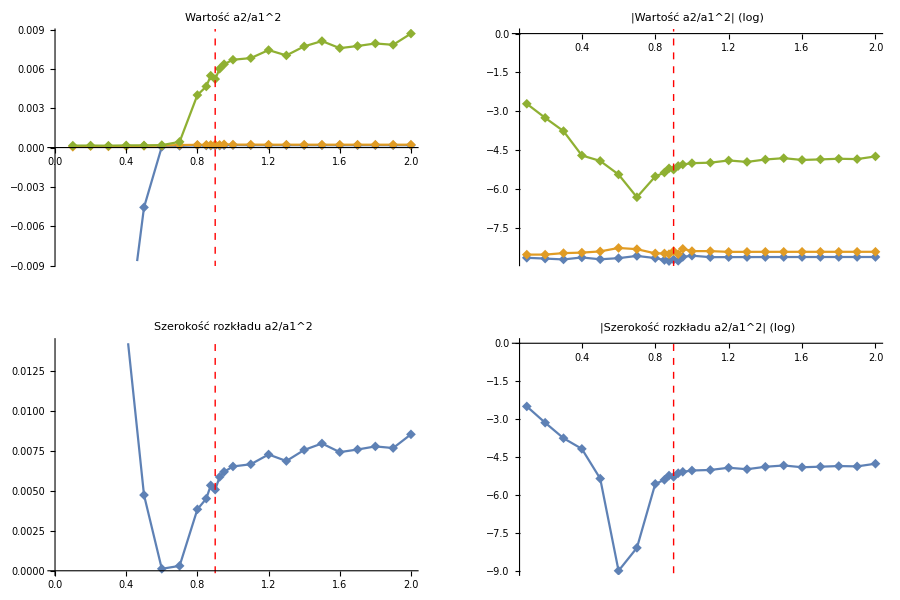

```mathematica
plota2Normalised[1,2,1,25]
plota2NormalisedWidth
GraphicsGrid[{{a2NormalisedPlot,a2NormalisedLogPLot},{a2NormalisedWidthPlot,a2NormalisedWidthLogPlot}},AspectRatio->1/1.5,Frame->All,ImageSize->900]
```

### River graph

```mathematica
plotSimData[data_, streamMin_, streamMax_,colour_:Black]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,data["Model", "width"]},{0,5.75}},
(*PlotRange->{{0,data["Model", "width"]},{0,data["Model", "height"]}},*) 
PlotLabel -> "Początkowa sieć rzeczna",
 ImageSize -> 400,
AspectRatio->1/1.5,
PlotRangePadding->0,

PlotStyle->Join[Table[colour,streamMin-1],Table[Blue,streamMax-streamMin+1],Table[colour,1]]];
```

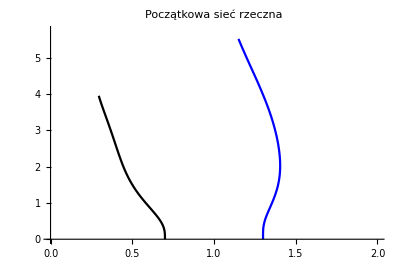

```mathematica
plotSimData[ImportJSONData[folder<>"/original_eta.json"],2,2]
```

```mathematica
plotRiver[streamMin_,streamMax_]:=Module[{},
riverPlot = plotSimData[ImportJSONData[folder<>"/original_eta.json"],streamMin, streamMax];
]
```

### Final results

```mathematica
replotFinal[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
plotGeoDev[streamMin,streamMax,stepMin,stepMax];
plotGeoDevWidth;
plotAngDev[streamMin,streamMax,stepMin,stepMax];
plotAngDevWidth;
plota2Normalised[streamMin,streamMax,stepMin,stepMax];
plota2NormalisedWidth;
plotRiver[streamMin,streamMax];
final=GraphicsGrid[{{riverPlot,geoDevLogPLot,geoDevWidthLogPlot},{angDevPlot,angDevLogPLot,angDevWidthLogPlot},{a2NormalisedPlot,a2NormalisedLogPLot,a2NormalisedWidthLogPlot}},ImageSize->1100,AspectRatio->1/1.5]
]

plotFinal:=Module[{},
final=GraphicsGrid[{{riverPlot,geoDevLogPLot,geoDevWidthLogPlot},{angDevPlot,angDevLogPLot,angDevWidthLogPlot},{a2NormalisedPlot,a2NormalisedLogPLot,a2NormalisedWidthLogPlot}},ImageSize->1100,AspectRatio->1/1.5]
]
```

### Simplified final

```mathematica
replotSimpFinal[streamMin_,streamMax_,stepMin_,stepMax_]:=Module[{},
plotGeoDev[streamMin,streamMax,stepMin,stepMax];
plotAngDev[streamMin,streamMax,stepMin,stepMax];
plota2Normalised[streamMin,streamMax,stepMin,stepMax];
simpFinal=GraphicsRow[{geoDevLogPLot,angDevPlot,a2NormalisedPlot},ImageSize->1100,AspectRatio->1/1.5]
]

plotSimpFinal:=Module[{},
simpFinal=GraphicsRow[{geoDevLogPLot,angDevPlot,a2NormalisedPlot},ImageSize->1100,AspectRatio->1/1.5]
]
```

## Setting initial parameters

## Results

### Setting experiment name and checking how many backwards steps do we have

```mathematica
experimentName="initialLength_back_3steps_corr";
```

```mathematica
(*initialization[etaOrigin_, etaMin_,etaMax_,fName_:"/back_lap"]*)
Do[initialization[i,1,20, experimentName];
Print["eta=",i/10.," -> ",Length/@backwardSimDataArray[[All,3,1,2,2,1]]],
{i,1,15}]
```

eta=0.1 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.2 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.3 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.4 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.5 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.6 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.7 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.8 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=0.9 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1. -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1.1 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1.2 -> {25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1.3 -> {23,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1.4 -> {19,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

eta=1.5 -> {16,23,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25}

{Number of steps exceeded in eta = ,{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}}}

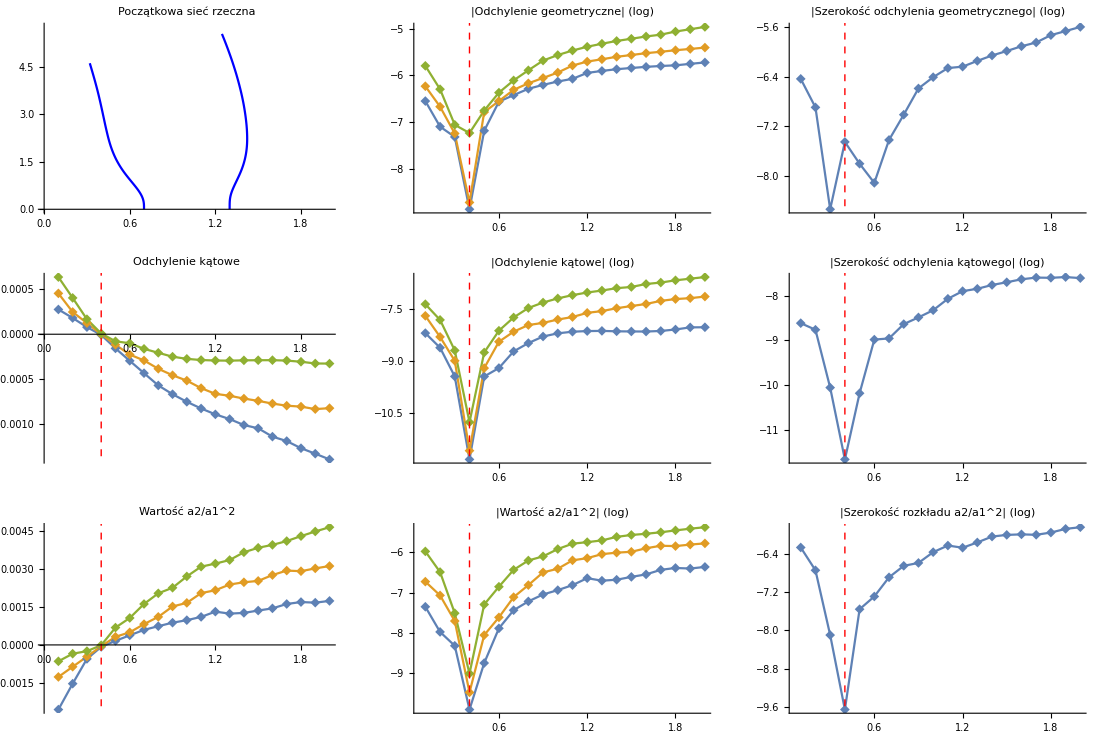

```mathematica
(*initialization[etaOrigin_, etaMin_,etaMax_,experimentName_,fileName_:"/back_lap"]*)
initialization[(*etaOrigin -> *) 4,(*etaMin -> *)1,(*etaMax -> *)20, experimentName]
(*replotFinal[streamMin_,streamMax_,stepMin_,stepMax_]*)
replotFinal[(*streamMin -> *)1,(*streamMax -> *)2,(*stepMin -> *)1,(*stepMax -> *)25]
```

#### Export .pdf

```mathematica
Do[
initialization[i,1,20, experimentName];
Export[experimentName<>"/pdf/lap"<>ToString[i]<>".pdf",replotFinal[1,2,1,10]];
,{i, 1,15}
]
```

{Number of steps exceeded in eta = ,{}}

{Number of steps exceeded in eta = ,{}}

{Number of steps exceeded in eta = ,{}}

«33 more identical outputs»

{Number of steps exceeded in eta = ,{{0.1}}}

{Number of steps exceeded in eta = ,{{0.1}}}

{Number of steps exceeded in eta = ,{{0.1}}}

«3 more identical outputs»

{Number of steps exceeded in eta = ,{{0.1,0.2}}}

{Number of steps exceeded in eta = ,{{0.1,0.2}}}

{Number of steps exceeded in eta = ,{{0.1,0.2}}}